# Chapter. Programming

##### Paul Abbott paul.c.abbott@uwa.edu.au

## Patterns with Constraints

Consider, again, the factorial function defined by the recursion relation

n!==n×(n-1)!
 0!==1

Here is a rule-based program for computing n!. This definition implies that n∈ℤ^+:

```mathematica
facRule[n_]:=n facRule[n-1]
```

```mathematica
facRule[0]=1
```

1

Compute 20!

```mathematica
facRule[20]
```

2432902008176640000

Compute 100! and check it.

```mathematica
facRule[100]==100!
```

True

```mathematica
facRule[a,b]
```

facRule(a,b)

### Allowed Function Arguments

What happens for negative arguments?

```mathematica
facRule[-1]
```

$RecursionLimit::reclim: Recursion depth of TraditionalForm`256 exceeded.

-3350850684932979117652665123754814942022584063591740702576779884286208799035732771005626138126763314259280802118502282445926550135522251856727692533193070412811083330325659322041700029792166250734253390513754466045711240338462701034020262992581378423147276636643647155396305352541105541439434840109915068285430675068591638581980604162940383356586739198268782104924614076605793562865241982176207428620969776803149467431386807972438247689158656000000000000000000000000000000000000000000000000000000000000000 Hold[facRule(-255-1)]

What happens for decimal arguments?

```mathematica
facRule[0.3]
```

$RecursionLimit::reclim: Recursion depth of TraditionalForm`256 exceeded.

5.76518629571408×10^500 Hold[facRule(-253.7-1)]

The recursive definition only works for non-negative integers. We need to incorporate conditions that check for the validity of the arguments. To do this we need a more restrictive patterns in the definition.

First we restrict the Head of the function argument n to be an Integer:

```mathematica
Head[3]
```

Integer

```mathematica
f[n_Integer]:=n
```

```mathematica
{f[2],f[2.],f[-2]}
```

{2,f(2.),-2}

Next we require the n to be positive using PatternTest (or ?) and the predicate Positive:

```mathematica
Clear[f]
```

```mathematica
f[n_Integer?Positive]:=n
```

```mathematica
{f[2],f[2.],f[-2]}
```

{2,f(2.),f(-2)}

What would happen if both these rules for f were active at the same time?

### Function Arguments

Mathematica does not require the user to specify the number or type of arguments of a function. Here are four reasons why:

It allows you to define and use Options;

It allows you to overload functions;

You can use of refer to functions before they are defined;

It allows you to call functions with unspecified arguments.

### Tracing Computations

To try to understand how a program works (or more importantly doesn't work), Mathematica includes a Trace function.

Trace the computation of facRule[5]:

```mathematica
Trace[facRule[5]]
```

{facRule(5),5 facRule(5-1),{{5-1,4},facRule(4),4 facRule(4-1),{{4-1,3},facRule(3),3 facRule(3-1),{{3-1,2},facRule(2),2 facRule(2-1),{{2-1,1},facRule(1),1 facRule(1-1),{{1-1,0},facRule(0),1},1 1,1},2 1,2},3 2,6},4 6,24},5 24,120}

View the output of Trace in TreeForm:

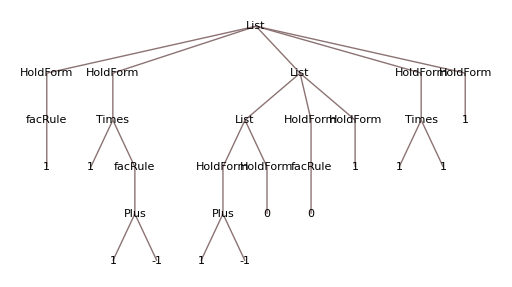

```mathematica
Trace[facRule[1]]//TreeForm
```

Trace can be restricted to only output steps associated with a particular symbol:

```mathematica
Trace[facRule[5],facRule]
```

{facRule(5),5 facRule(5-1),{facRule(4),4 facRule(4-1),{facRule(3),3 facRule(3-1),{facRule(2),2 facRule(2-1),{facRule(1),1 facRule(1-1),{facRule(0),1}}}}}}

Trace can select its output based on arbitrary patterns:

```mathematica
Trace[facRule[5],facRule[_]]
```

{facRule(5),{facRule(4),{facRule(3),{facRule(2),{facRule(1),{facRule(0)}}}}}}

```mathematica
Trace[facRule[5],facRule[n_/;n>3]]
```

{facRule(5),{facRule(4)}}

## Association

By default, a definition is associated with Head of the right-hand expression. Sometimes this is not what we want.

The following input tries to define a rule that uses linearity to simplify an expression:

```mathematica
Clear[g]
```

```mathematica
g[a_]+g[b_]:=g[a+b]
```

SetDelayed::write: Tag Plus in g[a_] + g[b_] is Protected.

$Failed

The problem is that the head of the LHS is Plus which is Protected:

```mathematica
Head[g[a_]+g[b_]]
```

Plus

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

What we want to do is associate the rule with g and to this we use TagSet or /:

```mathematica
g/:g[a_]+g[b_]:=g[a+b]
```

View the rules associated with g:

```mathematica
?g
```

Global`g

g[a_]+g[b_]^:=g[a+b]

Note that since Plus is associative (it has the Attribute of Orderless), the above rule will work on the sum of any number of terms:

```mathematica
g[a]+g[b]+g[c]
```

g(a+b+c)

Use Trace to see how this works.

```mathematica
Trace[g[a]+g[b]+g[c]]
```

{g(a)+g(b)+g(c),g(c)+g(a+b),g(a+b)+g(c),g((a+b)+c),{(a+b)+c,a+b+c},g(a+b+c)}

## Loops and Conditionals

The staple of procedural ‘traditional’ programming. Anyone who's programmed before will feel comfortable with these.

### Loops

In Mathematica there are the standard Looping Constructs, such as While[test,body] and For[start,test,incr,body], as well as ones associated with rule based and functional procedures.

Here is an example of using Do:

```mathematica
Do[Print[i],{i,1,5}]
```

1

2

3

4

5

Here is an example of using While:

```mathematica
i=1;While[i≤5,Print[i];i++]
```

1

2

3

4

5

```mathematica
i
```

6

Here is an example of using For:

```mathematica
i=.;For[i=1,i≤5,i++,Print[i]]
```

1

2

3

4

5

### Conditionals

The basic test is If. It has the form If[condition,t,f,u].

The other two conditionals used in programming are Which and Switch.

Here is a simple example of the use of If:

```mathematica
h[x_]:=If[x<2,"x is less than 2","x is not less than 2","it is unknown if x is less than 2"]
```

```mathematica
h[2]
```

x is not less than 2

```mathematica
h[1]
```

x is less than 2

```mathematica
h[a]
```

it is unknown if x is less than 2

Use Piecewise instead:

```mathematica
p[x_]=Piecewise[{{x,x>0},{-x,x<0},{1,x==0}}]
```

Piecewise[{{x, x>0}, {-x, x<0}, {1, x==0}}]

## Pure Functions

Pure Functions also known as anonymous functions embody the idea of a map.

Here is one way to implement the function f(x)=x^2:

```mathematica
f[x_]:=x^2
```

```mathematica
f[y]
```

y^2

```mathematica
Clear[f]
```

Implement the function f(x) as a map f:x↦x^2:

```mathematica
f=x↦x^2;
```

```mathematica
f[y]
```

y^2

```mathematica
f'
```

x↦2 x

In TraditionalForm Function[x,x^2] is displayed as x↦x^2.

Implement the map q:{x,y}↦x^y-y^x:

```mathematica
q={x,y}↦x^y-y^x
```

{x,y}↦x^y-y^x

```mathematica
q[a,b]
```

a^b-b^a

Solutions to DEs, obtained via DSolve[eqn,y,x], are replacement rules involving maps (or pure functions):

```mathematica
DSolve[{y'[x]==y[x]^2,y[0]==1},y,x]
```

{{y→({x}↦1/(1-x))}}

```mathematica
y[x]/.First[%]
```

1/(1-x)

Note that DSolve[eqn,y[x],x] gives solutions for y[x] rather than for the function y itself:

```mathematica
DSolve[{y'[x]==y[x]^2,y[0]==1},y[x],x]
```

{{y(x)→1/(1-x)}}

A pure function that squares and adds 1 to its argument:

```mathematica
(#^2+1&)[3]
```

10

```mathematica
(x↦x^2+1)[3]
```

10

A pure function that implements the map {x,y}↦x^y-y^x:

```mathematica
(#1^#2-#2^#1&)[a,b]
```

a^b-b^a

The notation (#^2&)[y] may look complicated, but it is similar to other mathematical notations such as∫f(x)ⅆx. The ∫ indicates the operation of integration, and the symbol following ⅆ (not the letter d) is the integration variable.

The roots of polynomials also involve maps, displayed using the short-hand form for Function:

```mathematica
Solve[x^5-x+1==0]
```

{{x→Root-1.17Root[1-#1+#1^5&,1]-1.1673039782614187},{x→Root-0.181-1.08 ⅈRoot[1-#1+#1^5&,2]-0.18123244446987538},{x→Root-0.181+1.08 ⅈRoot[1-#1+#1^5&,3]-0.18123244446987538},{x→Root0.765-0.352 ⅈRoot[1-#1+#1^5&,4]0.7648844336005847},{x→Root0.765+0.352 ⅈRoot[1-#1+#1^5&,5]0.7648844336005847}}

Here is the first root of the map x↦x^5-x+1:

```mathematica
Root[x↦x^5-x+1,1]
```

Root-1.17Root[1-#1+#1^5&,1]-1.1673039782614187

```mathematica
N[%,40]
```

-1.167303978261418684256045899854842180721

### PatternTest

Short pure functions are extremely useful as the predicate in a pattern:

```mathematica
Range[10]/.x_?(t↦t<4)->0
```

{0,0,0,4,5,6,7,8,9,10}

## Modules

There are times when you want to use “local” variables and definitions in a procedure; see Modules and Local Variables and the tutorial Modularity and the Naming of Things.

There are three commands that are used in different circumstances: With, Module and Block. For most purposes Module is appropriate, and so is the only one that we'll worry about.

## Constructing Simple Programs

A good approach to programming in Mathematica is to:

play around with the problem until you find a series of ‘steps’ that work;

test that these steps work in a variety of cases;

put them together in a Module or in a Functional program etc…

When just solving science and maths problems, most notebooks end up being a mix of all programming styles. You use whatever is the most appropriate, most obvious or the quickest for each step in the problem. It's only when you have to write a program which has to be run many times or with a lot of data, that you really need to think about optimising your code.